```mathematica
RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]
```

1200

1199

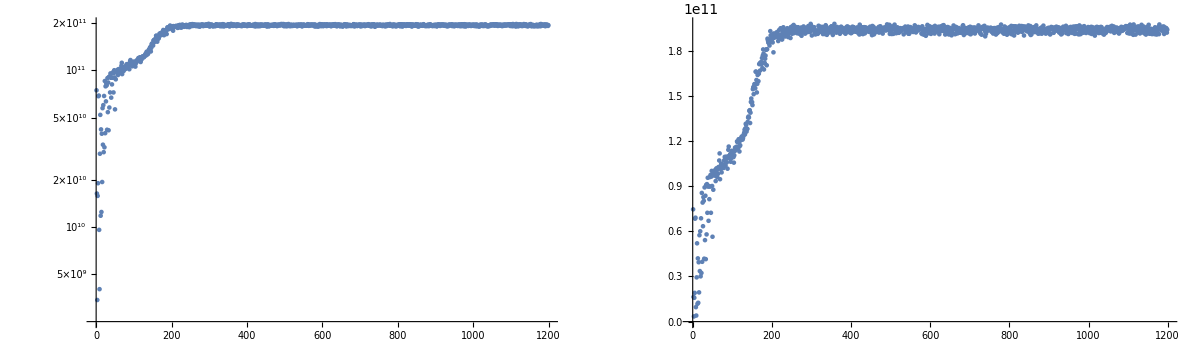

```mathematica
GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200]
```

### Live plot

```mathematica
(*Dynamic[livePlot]

makeLivePlot[]:=(
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];

livePlot = GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200];
)

task=CreateScheduledTask[makeLivePlot[],1]; (*Runs myFunction every 1 second*)
StartScheduledTask[task];*)
```

### Analyze

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]];
```

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

QA10361kG : -1.9935177
QA10371kG : 2.2916911267
QE10425kG : -0.5819683547
QE10441kG : 0.5627716142
QE10511kG : 0.3737291781
QE10525kG : 1.0542898666
twissCalculationFraction : 0.9
PDrive_mean_x : 0.0000152449
PDrive_mean_y : -7.073e-7
PDrive_sigma_x : 0.0000689481
PDrive_sigma_y : 0.0000788993
PDrive_mean_xp : -9.128e-7
PDrive_mean_yp : -1.38e-8
PDrive_twiss_beta_x : 6.3855588643
PDrive_twiss_alpha_x : -0.2573505106
PDrive_twiss_beta_y : 16.3340585834
PDrive_twiss_alpha_y : 1.229662747
PDrive_median_x : 0.0000206012
PDrive_median_y : 1.0641e-6
PDrive_median_xp : -6.764e-7
PDrive_median_yp : -1.628e-7
PDrive_emitSI_x : 6.8631e-6
PDrive_emitSI_y : 3.8103e-6
PDrive_norm_emit_x : 2.3995e-6
PDrive_norm_emit_y : 2.1178e-6
PDrive_BMAG_x : 1.5539253035
PDrive_BMAG_y : 1.3536316092
PDrive_BMAG_emit_x : 3.7287e-6
PDrive_BMAG_emit_y : 2.8668e-6
PDrive_BMAG_emitSI_x : 0.0000106648
PDrive_BMAG_emitSI_y : 5.1578e-6
PDrive_zCentroid : 926.0509884444
PWitness_mean_x : -0.0000700134
PWitness_mean_y : -0.0000127675
PWitness_sigma_x : 0.0000766043
PWitness_sigma_y : 0.0001292715
PWitness_mean_xp : 2.2126e-6
PWitness_mean_yp : 2.932e-7
PWitness_twiss_beta_x : 26.5975451701
PWitness_twiss_alpha_x : 1.8033384877
PWitness_twiss_beta_y : 73.7503215058
PWitness_twiss_alpha_y : 2.3600857533
PWitness_median_x : -0.0000803591
PWitness_median_y : -9.6138e-6
PWitness_median_xp : 2.3095e-6
PWitness_median_yp : 3.992e-7
PWitness_emitSI_x : 3.4491e-6
PWitness_emitSI_y : 3.323e-6
PWitness_norm_emit_x : 2.084e-6
PWitness_norm_emit_y : 1.8859e-6
PWitness_BMAG_x : 1.3799480109
PWitness_BMAG_y : 1.6797013696
PWitness_BMAG_emit_x : 2.8759e-6
PWitness_BMAG_emit_y : 3.1677e-6
PWitness_BMAG_emitSI_x : 4.7596e-6
PWitness_BMAG_emitSI_y : 5.5816e-6
PWitness_zCentroid : 926.051160711
bunchSpacing : 0.0001722666
transverseCentroidOffset : 0.0000861071
lostChargeFraction : 0.
errorTerm_lostChargeFraction : 0.
errorTerm_mainObjective : 0.
maximizeMe : 1.97890496827486297607e11

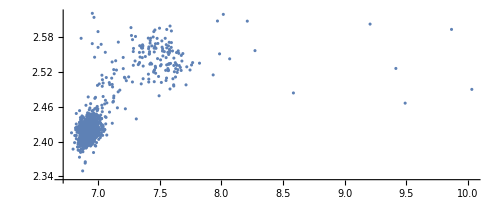

```mathematica
Show[
ListPlot[{
10^6#["PDrive_emitSI_x"],
10^6#["PDrive_norm_emit_x"]
}&/@raw,
AspectRatio->Automatic,PlotRange->All],
Plot[x,{x,0,50},PlotStyle->Red]
]
```

## Plot all

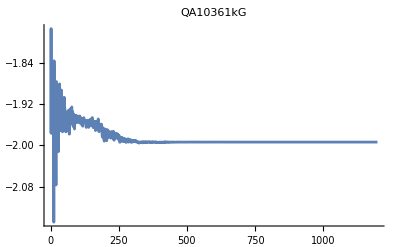
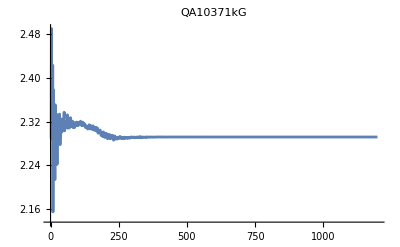
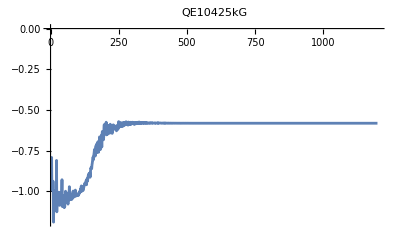
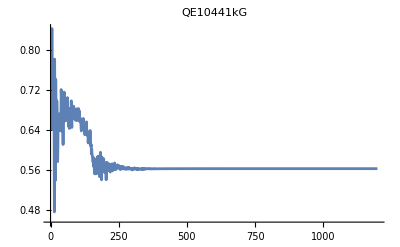
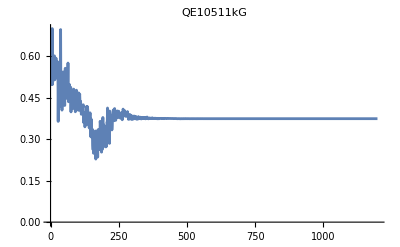
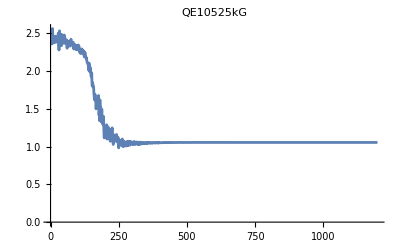
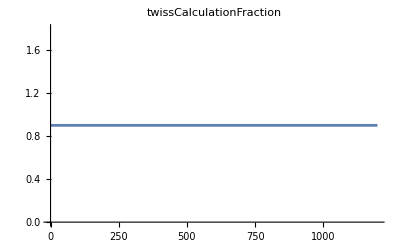
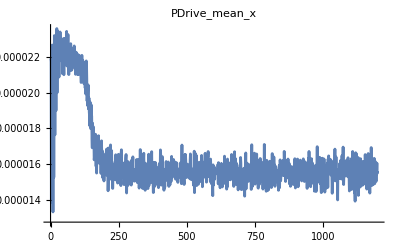
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 0

```mathematica
imgArr=Table[
ListPlot[
raw[[All,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"QA10361kG","QA10371kG","QE10425kG","QE10441kG","QE10511kG","QE10525kG","L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{QA10361kG,QA10371kG,QE10425kG,QE10441kG,QE10511kG,QE10525kG}

```mathematica
fitVar = "PDrive_twiss_beta_x"
(*fitVar = "bunchSpacing"*)
```

PDrive_twiss_beta_x

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

FittedModel[…]

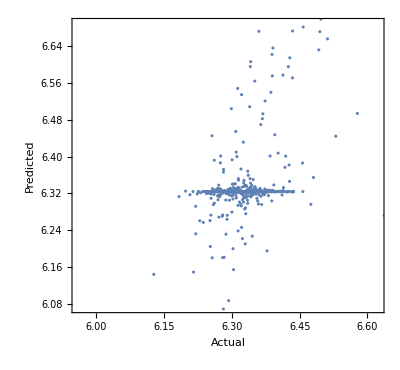

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
lm["ANOVATable"]
```

General::munfl: Exp[-1770.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2045.92] is too small to represent as a normalized machine number; precision may be lost.

| DF | SS | MS | F-Statistic | P-Value
QA10361kG | 1 | 2126.02 | 2126.02 | 21893.3 | 0.
QA10371kG | 1 | 76.1766 | 76.1766 | 784.452 | 4.74533×10^-133
QE10425kG | 1 | 3445.7 | 3445.7 | 35483.1 | 0.
QE10441kG | 1 | 3.3455 | 3.3455 | 34.4513 | 5.65863×10^-9
QE10511kG | 1 | 132.812 | 132.812 | 1367.67 | 4.81001×10^-200
QE10525kG | 1 | 85.9012 | 85.9012 | 884.594 | 7.37341×10^-146
Error | 1192 | 115.753 | 0.0971081 |  | 
Total | 1198 | 5985.71 |  |  |

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["New spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | New spacing | Delta
L0BPhaseSet | -1.72103 | Missing[KeyAbsent,L0BPhaseSet] | 1.72103+Missing[KeyAbsent,L0BPhaseSet]
L1PhaseSet | -20.312 | Missing[KeyAbsent,L1PhaseSet] | 20.312+Missing[KeyAbsent,L1PhaseSet]
L2PhaseSet | -38.6737 | Missing[KeyAbsent,L2PhaseSet] | 38.6737+Missing[KeyAbsent,L2PhaseSet]
L3PhaseSet | -1.46329 | Missing[KeyAbsent,L3PhaseSet] | 1.46329+Missing[KeyAbsent,L3PhaseSet]
S1EL_xOffset | 0.000385255 | Missing[KeyAbsent,S1EL_xOffset] | -0.000385255+Missing[KeyAbsent,S1EL_xOffset]
S1EL_yOffset | -0.000241114 | Missing[KeyAbsent,S1EL_yOffset] | 0.000241114+Missing[KeyAbsent,S1EL_yOffset]
S2EL_xOffset | -0.00141787 | Missing[KeyAbsent,S2EL_xOffset] | 0.00141787+Missing[KeyAbsent,S2EL_xOffset]
S2EL_yOffset | 0.0000111705 | Missing[KeyAbsent,S2EL_yOffset] | -0.0000111705+Missing[KeyAbsent,S2EL_yOffset]
S2ER_xOffset | -0.00223816 | Missing[KeyAbsent,S2ER_xOffset] | 0.00223816+Missing[KeyAbsent,S2ER_xOffset]
S2ER_yOffset | -0.000675996 | Missing[KeyAbsent,S2ER_yOffset] | 0.000675996+Missing[KeyAbsent,S2ER_yOffset]
S1ER_xOffset | 0.00100714 | Missing[KeyAbsent,S1ER_xOffset] | -0.00100714+Missing[KeyAbsent,S1ER_xOffset]
S1ER_yOffset | 0.000398456 | Missing[KeyAbsent,S1ER_yOffset] | -0.000398456+Missing[KeyAbsent,S1ER_yOffset]
XC1FFkG | 0.206455 | Missing[KeyAbsent,XC1FFkG] | -0.206455+Missing[KeyAbsent,XC1FFkG]
XC3FFkG | -0.0899164 | Missing[KeyAbsent,XC3FFkG] | 0.0899164+Missing[KeyAbsent,XC3FFkG]
YC1FFkG | -0.0022312 | Missing[KeyAbsent,YC1FFkG] | 0.0022312+Missing[KeyAbsent,YC1FFkG]
YC2FFkG | -0.00851158 | Missing[KeyAbsent,YC2FFkG] | 0.00851158+Missing[KeyAbsent,YC2FFkG]